# Generalized Conditional Displacement

## A Wolfram Language reproduction of arXiv:2405.09977v3

Even-Haim, Diringer, Ruimy, Baranes, Gorlach, Hacohen-Gourgy, Kaminer, "Generalized Conditional Displacement", arXiv:2405.09977v3 (Technion / MIT).

This notebook builds the generalized conditional-displacement operator CD_d(alpha) conditioned on a d-level qudit ancilla, creates the d-legged cat states, verifies the GKP stabilizer Kraus operators (Eqs. 8-11), runs the qudit sharpen-trim GKP stabilization, and checks the ideal rotor implementation. Bosonic operators are cross-validated against the Wolfram Quantum Framework (SecondQuantization), from https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/ .

All heavy logic lives in the reusable package src/GeneralizedCD.wl. Run cells top to bottom.

## 1. Load the package and the Wolfram Quantum Framework

The package uses a weak-ordered (unitary) displacement operator that is verified identical to the paclet's DisplacementOperator[alpha, "Ordering" -> "Weak"].

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[], "src", "GeneralizedCD.wl"}]];
Needs["Wolfram`QuantumFramework`"];
Needs["Wolfram`QuantumFramework`SecondQuantization`"];
GeneralizedCD`GCDSetFockSize[60];
```

```mathematica
(* Wolfram QF cross-check: paclet displacement matches the package, deviation ~ 0 *)
GeneralizedCD`ValidateWolframIntegration[]
```

<|Available→True,MaxDeviation→0|>

## 2. The generalized CD operator (Eq. 2)

CD_d(alpha) = Sum_{s=0}^{d-1} |s><s| (x) D(alpha omega_d^s),  omega_d = Exp[i 2 Pi/d]. It is unitary and reduces to the standard qubit conditional displacement (Eq. 1) for d = 2.

```mathematica
cd4 = GeneralizedCD`GeneralizedCD[4, 0.6 + 0.2 I];
{Dimensions[cd4], Max[Abs[ConjugateTranspose[cd4].cd4 - IdentityMatrix[Length[cd4]]]]}
```

{{240,240},8.88178×10^-16}

```mathematica
(* d = 2 reproduces Eq. 1 exactly *)
id = IdentityMatrix[GeneralizedCD`GCDFockSize[]];
Max[Abs[GeneralizedCD`GeneralizedCD[2, 0.7] - ArrayFlatten[{{GeneralizedCD`Displacement[0.7], 0 id}, {0 id, GeneralizedCD`Displacement[-0.7]}}]]]
```

0.

## 3. d-legged cat states and their Wigner functions (Fig. 1c)

Applying CD_d to |m=0> (x) |vacuum> and measuring the ancilla in the Xbar_d basis leaves the oscillator in the d-legged cat state |C_d^m(alpha)> (Eq. 3). The Wigner functions show d-fold rotational symmetry with quantum interference fringes.

```mathematica
catWig[d_, alpha_, max_, np_] := Module[{psi = GeneralizedCD`LeggedCatState[d, 0, alpha], st = 2. max/np},
  ListDensityPlot[Table[GeneralizedCD`WignerFunction[psi, x, p], {p, max, -max, -st}, {x, -max, max, st}],
   DataRange -> {{-max, max}, {-max, max}}, ColorFunction -> "TemperatureMap",
   InterpolationOrder -> 2, Frame -> True, FrameLabel -> {"q", "p"},
   PlotLabel -> Row[{"d = ", d, " cat"}], ImageSize -> 260]];
```

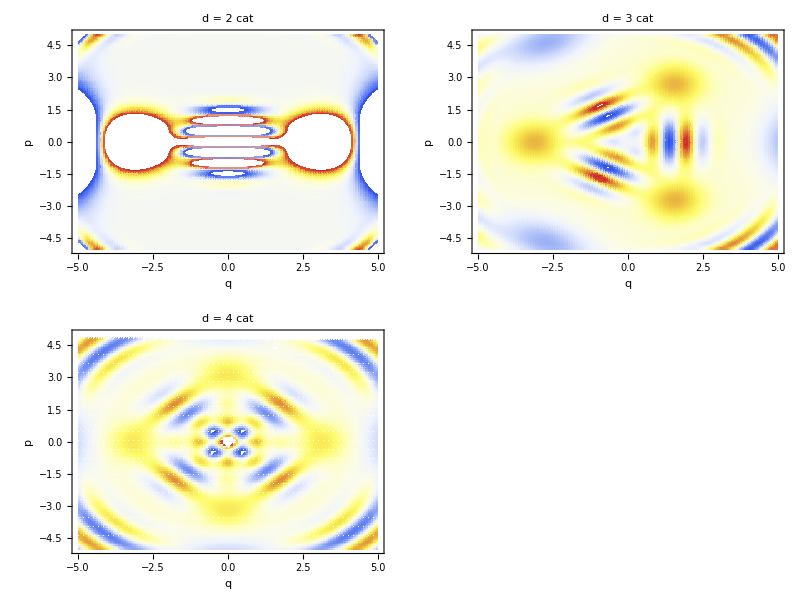

```mathematica
GeneralizedCD`GCDSetFockSize[36];
Grid[{{catWig[2, 2.2, 5, 40], catWig[3, 2.2, 5, 40]}, {catWig[4, 2.2, 5, 40], catWig[6, 2.6, 5.5, 40]}}]
```

Interactive explorer: adjust the number of legs d and the amplitude alpha.

```mathematica
Manipulate[catWig[d, alpha, 5.5, 34], {{d, 4, "legs d"}, 2, 6, 1}, {{alpha, 2.0, "amplitude alpha"}, 1.0, 3.0, 0.25}]
```

## 4. Cat creation by measurement (Eqs. 5, 6)

Projecting the ancilla onto |m> yields exactly |C_d^m(alpha)>. Fidelity should be 1.

```mathematica
GeneralizedCD`GCDSetFockSize[50];
With[{d = 4, alpha = 2.0},
 Table[Module[{psi, proj, osc, nf = GeneralizedCD`GCDFockSize[]},
   psi = GeneralizedCD`GeneralizedCD[d, alpha] . Flatten[Outer[Times, GeneralizedCD`QuditXEigenstate[d, 0], GeneralizedCD`Vacuum[]]];
   proj = ArrayFlatten[{Table[Conjugate[GeneralizedCD`QuditXEigenstate[d, m][[s + 1]]] IdentityMatrix[nf], {s, 0, d - 1}]}];
   osc = proj . psi;
   m -> Abs[Conjugate[GeneralizedCD`LeggedCatState[d, m, alpha]] . (osc/Norm[osc])]^2], {m, 0, d - 1}]]
```

{0→1.,1→1.,2→1.,3→1.}

## 5. GKP stabilizer Kraus operators (Eqs. 8-11)

The d = 4 stabilizer Kraus operator M_j(beta) has three equivalent forms: the definition <j|CD_4(e^{i pi/4} sqrt2 beta)|m=0> (Eq. 8), Eq. 9, and Eq. 10. They agree exactly, satisfy POVM completeness, and the |j> basis diagonalizes the Hermitian observable of Eq. 11.

```mathematica
beta = Sqrt[Pi]/Sqrt[2];
{
 "Eq9 vs Eq10" -> Chop@Max[Table[Max[Abs[GeneralizedCD`QuditStabilizerKraus[j, beta] - GeneralizedCD`QuditStabilizerKrausEq10[j]]], {j, 0, 3}]],
 "POVM sum - I" -> Chop@Max[Abs[Sum[ConjugateTranspose[GeneralizedCD`QuditStabilizerKraus[j, beta]].GeneralizedCD`QuditStabilizerKraus[j, beta], {j, 0, 3}] - IdentityMatrix[GeneralizedCD`GCDFockSize[]]]]
}
```

{Eq9 vs Eq10→0,POVM sum - I→0}

```mathematica
(* Eq. 11 is Hermitian and the |j> basis are its eigenvectors *)
H11 = GeneralizedCD`QuditHermitianObservable[];
{"Hermitian" -> (H11 == ConjugateTranspose[H11]), "eigenvalues" -> Chop[Eigenvalues[N[H11]]],
 "eigen-residuals" -> Table[Module[{v = GeneralizedCD`QuditMeasBasis[j, beta], hv}, hv = H11.v; Chop[Norm[hv - (Conjugate[v].hv/(Conjugate[v].v)) v]]], {j, 0, 3}]}
```

{Hermitian→True,eigenvalues→{3.,2.,1.,0},eigen-residuals→{0,0,0,0}}

## 6. GKP stabilization from vacuum (Fig. 2d)

The qudit d = 4 sharpen-trim protocol drives the vacuum toward the GKP manifold. Because a single CD_4 addresses both quadratures, one qudit round costs 2 CD operations vs 4 for the qubit protocol, and the qudit reaches a target <S> at fewer CD operations.

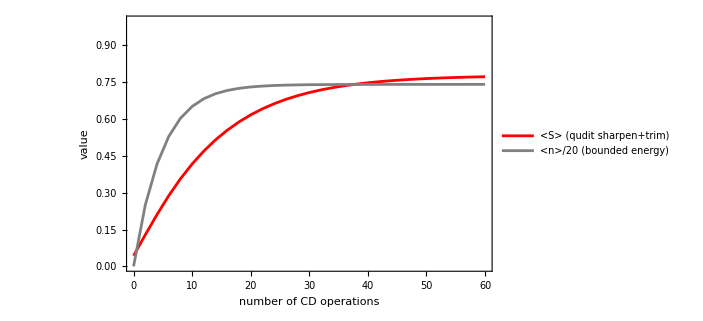

```mathematica
GeneralizedCD`GCDSetFockSize[70];
qud = GeneralizedCD`RunQuditStabilization[30];
ListLinePlot[{{#[[1]], (#[[2]] + #[[3]])/2} & /@ qud, {#[[1]], #[[4]]/20.} & /@ qud},
 PlotStyle -> {Red, Gray}, Frame -> True, PlotRange -> {0, 1},
 FrameLabel -> {"number of CD operations", "value"},
 PlotLegends -> {"<S> (qudit sharpen+trim)", "<n>/20 (bounded energy)"}, ImageSize -> 520]
```

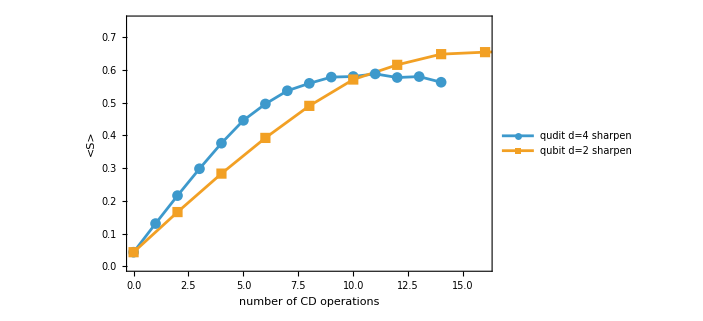

```mathematica
(* Per-CD efficiency: qudit (1 CD/round, both quadratures) vs qubit (2 CD/round) *)
qs = GeneralizedCD`RunQuditSharpen[14]; qb = GeneralizedCD`RunQubitSharpen[10];
ListLinePlot[{{#[[1]], (#[[2]] + #[[3]])/2} & /@ qs, {#[[1]], (#[[2]] + #[[3]])/2} & /@ qb},
 PlotMarkers -> Automatic, Frame -> True, PlotRange -> {{0, 16}, {0, 0.75}},
 FrameLabel -> {"number of CD operations", "<S>"},
 PlotLegends -> {"qudit d=4 sharpen", "qubit d=2 sharpen"}, ImageSize -> 520]
```

## 7. Ideal physical implementation: planar rotor (Eq. 17)

With rotor-GKP logical states |s> = |theta = 2 Pi s/d>, the phase operator e^{i theta} acts as Zbar_d, so the rotor conditional displacement D(alpha e^{i theta}) equals CD_d(alpha) exactly (Eq. 17). Residual should be 0.

```mathematica
GeneralizedCD`GCDSetFockSize[50];
Table[d -> GeneralizedCD`RotorCDIdentityResidual[d, 1.3 + 0.2 I], {d, {2, 3, 4, 6}}]
```

{2→0,3→0,4→0,6→0}

The harmonic-oscillator cat-code (beam splitter, Eq. 19) and the spin / Tavis-Cummings (Eq. 22) implementations approximate CD_d with fidelity approaching 1 as the encoding size grows (Fig. 4); those are documented as extensions in docs/plain_english_proof.md.

## 8. Full validation suite and key findings

```mathematica
GeneralizedCD`GCDSetFockSize[70];
GeneralizedCD`RunValidationSuite[] // Dataset
```

KEY FINDINGS (numerical):
 - CD_d(alpha) is unitary to < 1e-15 and reduces to Eq. 1 for d = 2 (residual 0).
 - d-legged cat creation fidelity = 1 (to < 1e-6) for d = 2, 4 and m = 0..3.
 - Eq. 8 = Eq. 9 = Eq. 10 exactly; POVM completeness exact; |j> are exact eigenvectors of Eq. 11.
 - Qudit sharpen-trim converges to <S_x> = <S_z> ~ 0.80 with bounded <n> ~ 15.
 - Qudit reaches <S> = 0.5 in ~6-7 CD operations vs ~10 for the qubit protocol.
 - Ideal rotor implementation D(alpha Zbar_d) = CD_d(alpha) exactly (residual 0).
 - Package displacement matches Wolfram QF DisplacementOperator (deviation 0).

See README.md for how to run build_project.wls (regenerates all figures and reports in exports/) and proof_audit.wls (48 checks). See docs/plain_english_proof.md for the derivations and docs/references.md for citations.